# Report Project 3

Course code: IX1500
Date: 2018-10-24

Rikard Jakobsson, rikjak@kth.se

Task 1: Dijkstra

## Summary

### Task

a) Explain how Dijkstra’s algorithm works. Use Mathematica graph-methods to illustrate your explanation with an animation.

### Result

Dijskstra’s algorithm finds the shortest path between two vertices in a graph by using a version of a breath first search. You start by marking the distance to all nodes directly reachable from the start node in a list, and setting the rest to infinity. You then add the reachable ones to a priority queue. For each element in the priority queue you check its adjacent nodes. If the distance to one of these is bigger than the current distance plus the distance there from the current node you update it and add the current node as the ‘parent’ to the node looked at. When this is done you can recursively get the shortest path to a node from the start node.

## Code

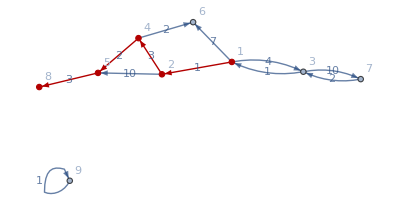

{0,1,4,6,4,6,14,9,∞}

{1,1,1,5,2,5,3,6,0}

{1,{1},2,{2,3,4},3,{3,4,5,6},4,{4,5,6,7},5,{5,6,7},6,{6,7,6},7,{7,6,8},6,{6,8},8,{8,8},8,{8}}

{1,3,7}

{1,3,7}

```mathematica
g = Graph[{1->2,1->3,1->6,2->4,2->5,3->7,3->1,4->5,4->6,5->8,7->3,9->9},EdgeWeight->{1,4,7,3,10,10,1,2,2,3,2,1},VertexLabels->Automatic,EdgeLabels->"EdgeWeight"];

HighlightGraph[g,PathGraph[FindShortestPath[g,1,8,Method->"Dijkstra"],DirectedEdges->True]]
distance = {};
parent = {};
test = {};
path ={};
dijkstra[graph_,from_,to_]:= (parent = ConstantArray[0,Length[VertexList[graph]]];
path ={};
queue = {};
visited={};
vl = VertexList[graph];
distance =ConstantArray[Infinity,Length[VertexList[graph]]];
adjacent =Normal[WeightedAdjacencyMatrix[graph]];
parent[[from]] =from;
distance[[from]] = 0;
addToQueue[from];
While[Length[queue]>0,(
element =queue[[1]];
AppendTo[visited,element];
AppendTo[test,element];
AppendTo[test,queue];
fillDistance[element,element];
); queue = Delete[queue,1];
];
(*fillDistance[from,from];*)

addToQueue[node_]:=(AppendTo[queue,node];
Sort[queue,distance[[#1]]<distance[[#2]]&];
);
getFromQueue[]:=(
a  = queue[[1]];
queue =Delete[queue,1];
Return[a]
);
fillDistance[input_,row_]:=(For[i = 1,i<Length[adjacent[[row]]],i++,
If[adjacent[[row]][[i]]≠0,
(If[distance [[i]]>(adjacent[[row]][[i]]+distance[[row]]),
(distance [[i]]=(adjacent[[row]][[i]]+distance[[row]]);
parent[[i]]=input)];
If[Not[MemberQ[visited,i]],addToQueue[i]]);

];
]);
p = parent[[to]];
AppendTo[path,vl[[to]]];
While[p≠from,(AppendTo[path,vl[[p]]]
);p = parent[[p]]];
AppendTo[path,vl[[from]]];
path = Reverse[path];
);
dijkstra[g,1,7];

distance
parent
test
path
FindShortestPath[g,1,7]
```